```mathematica
(* Grafico de soluciones de la Ecuacion de Boltzmann para desacoplo
      de Materia Oscura Fría (CDM) -particulas con masa. *)

(* La ecuacion considera la expansion del Universo y colisiones de desintegracion de las particulas de CDM en particulas standard o de mayor interaccion, que mantienen la distribucion de equilibrio 
aun despues de que la CDM se desacopla.*)

(* El grafico muestra 3 curvas, para distintas probabilidades de colision <σv>. Se considera el caso 
sólo para <σv> independiente de x (= m/T) relacionada al tiempo en la epoca  de radiación) *)

(* Ecuacion de Boltzmann:
dY/dx = λ/x^2 * (Y_eq^2 - Y^2 ) *)
(* donde λ es un parámetro adimensional, proporcional a la masa y a la seccion eficaz
              λ ~ m <σv>
Variables:
     y(x): yield (densidad numérica de CDM por unidad de densidad de entropía .. 
      normalizada de modo que Y(x) = a y(x)  
x = m/T : variable independiente, proporcional a t^(1/2) en la epoca de radiacion.
yeq[x]: distribucion de equilibrio térmico para partículas no relativistas *) 
(* Constantes:
λ es la tasa de interaccion respecto a la expansion de Hubble:
λ = s(m) <σv>/H(m) = 0,263 g*s M_planck m <σv>/sqrt(g* )
          ... con g*s = g* = 70,25 queda:
λ = 2,21 (m/GeV) (<σv>/10^-36 cm^3/s) 

"a" es la norma de la funcion de yield: Y(x) = a y(x)
a= 0,145 g/g*s .... donde usamos g=1 para CDM escalar y g*s = 70,25:
  a= 2,06x10^-3

λa = λ·a es la tasa de interaccion normalizada:
λa = 4,54 (m/GeV) ((<σv>/10^-33 cm^3/s)
```

```mathematica
yeq[x_] := x^(3/2) Exp[-x] (* Distribución de equilibrio térmico no-relativista, normalizada *)
```

```mathematica
Print[{yeq[1.], yeq[500.]}] (* valores extremos de yeq *)
```

```mathematica
λ=10^20;
s= NDSolve[{y'[x]== λ/x^2 *( yeq[x]^2 - y[x]^2),y[1]== 368/1000},y,{x,1,500},Method->{"StiffnessSwitching","NonstiffTest"->False},WorkingPrecision->40,PrecisionGoal->30,MaxSteps->10^6];
(* Resuelve la Ec. de Boltzmann para λa = 10^20 *)
```

```mathematica
λ1=10^15;
s1= NDSolve[{y1'[x]== λ1/x^2 *( yeq[x]^2 - y1[x]^2),y1[1]== 368/1000},y1,{x,1,500},Method->{"StiffnessSwitching","NonstiffTest"->False},WorkingPrecision->30];
(* Resuelve la Ec. de Boltzmann para λa = 10^15 *)
```

```mathematica
λ2=10^10;
s2= NDSolve[{y2'[x]== λ2/x^2 *( yeq[x]^2 - y2[x]^2),y2[1]== 368/1000},y2,{x,1,500},Method->{"StiffnessSwitching","NonstiffTest"->False},WorkingPrecision->20];
(* Resuelve la Ec. de Boltzmann para λa = 10^10 *)
```

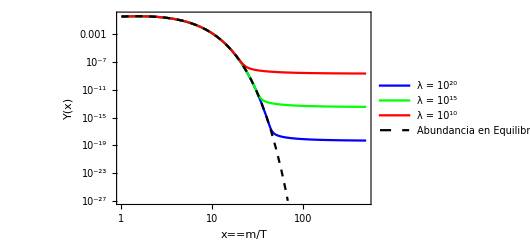

```mathematica
LogLogPlot[{Evaluate[y[x]/.s],Evaluate[y1[x]/.s1],Evaluate[y2[x]/.s2],yeq[x]},{x,1,500},PlotRange->{{1,500},{1,10^-27}},PlotStyle->{Blue,Green,Red,{Dashed,Black}},PlotTheme->"Scientific",PlotLegends->{"λ = 10^20","λ = 10^15","λ = 10^10","Abundancia en Equilibrio"},FrameLabel->{Style[,Black,15],Style[,Black,15]},FrameStyle->Black]
```

```mathematica
(*Resolución con cambio de variable W=ln(Y(x))*)

(*Este método es útil para disminuir la carga computacional. Se alcanza un orden de λa=10^11 sin necesidad de modificar la precisión de los cálculos manualmente, a diferencia del método anterior que se alcanza hasta λa=10^8.*)
```

```mathematica
yeq[x_] := x^(3/2) Exp[-x] (* Distribución de equilibrio térmico no-relativista, normalizada *)
Weq[x_]:=Log[yeq[x]];
Weq[1]
```

-1

```mathematica
λ=10^11;
s= NDSolve[{W'[x]== λ/x^2 *( Exp[2Weq[x]-W[x]]-Exp[W[x]]),W[1]== -1},W,{x,1,500}]
(* Resuelve la Ec. de Boltzmann para λa = 10^20 *)
y[x_]:=Exp[W[x]/.s]
```

{{W→InterpolatingFunction[…]}}

```mathematica
λ1=10^7;
s1= NDSolve[{W1'[x]== λ1/x^2 *( Exp[2Weq[x]-W1[x]]-Exp[W1[x]]),W1[1]== -1},W1,{x,1,500}]
(* Resuelve la Ec. de Boltzmann para λa = 10^20 *)
y1[x_]:=Exp[W1[x]/.s1]
```

{{W1→InterpolatingFunction[…]}}

```mathematica
λ2=10^5;
s2= NDSolve[{W2'[x]== λ2/x^2 *( Exp[2Weq[x]-W2[x]]-Exp[W2[x]]),W2[1]== -1},W2,{x,1,500}]
(* Resuelve la Ec. de Boltzmann para λa = 10^20 *)
y2[x_]:=Exp[W2[x]/.s2]
```

{{W2→InterpolatingFunction[…]}}

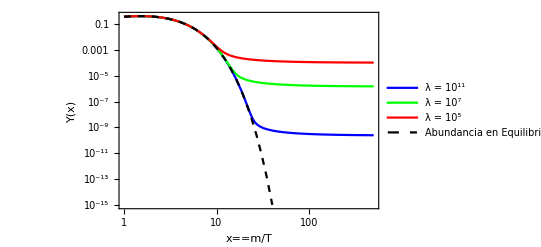

```mathematica
LogLogPlot[{Evaluate[y[x]/.s],Evaluate[y1[x]/.s1],Evaluate[y2[x]/.s2],yeq[x]},{x,1,500},PlotRange->{{1,200},{1,10^-15}},PlotStyle->{Blue,Green,Red,{Dashed,Black}},PlotTheme->"Scientific",PlotLegends->{"λ = 10^11","λ = 10^7","λ = 10^5","Abundancia en Equilibrio"},FrameLabel->{Style[,Black,15],Style[,Black,15]},FrameStyle->Black]
```

```mathematica
Clear["Global`*"]
```